## Zero-twist Bilayer, Isotropic Forces

```mathematica
ClearAll[ex, ey, n, latticepts,unitcellpts,dcutoff,bonds,segmentn,segments,qloop, freqs,D3x3]
```

## Layer Parameters

```mathematica
ex={1,0,0};
ey={0,1,0};
```

## Create Lattice and unit cell

```mathematica
n=50;
h=1;
latticepts={};
unitcellpts={{0,0,0},{0,0,h}};
For[i=-n/2,i<=n/2,i++,
For[j=-n/2,j<=n/2,j++,
AppendTo[latticepts, i*ex+j*ey+unitcellpts[[1]]];
AppendTo[latticepts, i*ex+j*ey+unitcellpts[[2]]];
]
]
ListPointPlot3D[latticepts]
```

-Graphics3D-

## Generate Adjacent Unit Cells

```mathematica
dcutoff = √2;
(*Bilayer*)
unitcells={};
xmin =Min[(unitcellpts.ex)/(√(ex.ex))]-dcutoff;
xmax =Max[(unitcellpts.ex)/(√(ex.ex))]+dcutoff;
ymin=Min[(unitcellpts.ey)/(√(ey.ey))]-dcutoff;
ymax=Max[(unitcellpts.ey)/(√(ey.ey))]+dcutoff;
nxmin=Floor[xmin/(√(ex.ex))];
nxmax = Ceiling[xmax/(√(ex.ex))];
nymin=Floor[ymin/(√(ey.ey))];
nymax=Ceiling[ymax/(√(ey.ey))];
For[i=nxmin,i<=nxmax,i++,
For[j=nymin,j<=nymax,j++,
AppendTo[unitcells, i*ex + j*ey]
];
];
```

## Create List of Bonds Included

```mathematica
bonds={};
bondgraphics={};
Monitor[For[i=1,i<=Length[unitcellpts],i++,
For[j=1,j<=Length[unitcellpts],j++,
For[R=1,R<=Length[unitcells],R++,
d=Norm[unitcellpts[[j]]+unitcells[[R]]-unitcellpts[[i]]];
If[d!=0&&d<=dcutoff,
dhat=1/d*(unitcellpts[[j]]+unitcells[[R]]-unitcellpts[[i]]);
AppendTo[bonds,{i, j,R,dhat,d}];
AppendTo[bondgraphics,Line[{unitcellpts[[i]],unitcellpts[[j]]+unitcells[[R]]}]];
];
]
]
],{i,j}]
Show[Graphics3D[bondgraphics],ListPointPlot3D[unitcellpts]]
```

-Graphics3D-

## Create Momentum Loop

```mathematica
segmentn=20;
segments={{0,0,0},{π,0,0},{π,π,0},{0,0,0}};
qloop={};
For[s=1,s<Length[segments],s++,
For[i=1,i<=segmentn,i++,
AppendTo[qloop,segments[[s]]+i*((segments[[s+1]]-segments[[s]])/segmentn)]
]
]
ListPointPlot3D[qloop]
```

-Graphics3D-

## Main Loop

```mathematica
freqs={};
A=.1;
λ=1/(.25);
Monitor[For[k=1,k<=Length[qloop],k++,
(*Momentum*)
q=qloop[[k]]; 
(*Dynamics Matrixes*)
DynamicsMatrix=ConstantArray[0,{3*Length[unitcellpts],3*Length[unitcellpts]}];
(*Loop over bonds*)
For[i=1,i<=Length[bonds],i++,
a1=bonds[[i]][[1]];
a2=bonds[[i]][[2]];
R=bonds[[i]][[3]];
dhat=bonds[[i]][[4]];
d=bonds[[i]][[5]];
D3x3=A*ⅇ^(-λ*d){{1,0,0},{0,1,0},{0,0,1}};
DynamicsMatrix[[3a1-2;;3a1,3a1-2;;3a1]]+=1*D3x3;
DynamicsMatrix[[3a1-2;;3a1,3a2-2;;3a2]]+=-D3x3*ⅇ^(I*unitcells[[R]].q);
];
AppendTo[freqs,√(Eigenvalues[DynamicsMatrix])]
]
,{k}]
```

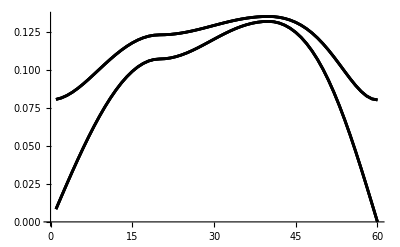

```mathematica
ListLinePlot[Table[freqs[[;;,i]],{i,1,3*Length[unitcellpts]}],PlotStyle->{{Black}},PlotRange->All]
```

## Analytic Results

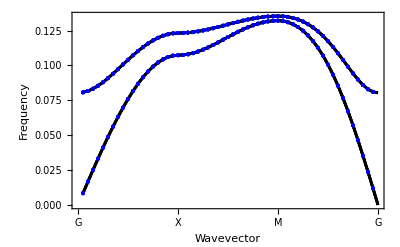

```mathematica
C1=A*ⅇ^-λ+A*Sum[ⅇ^(-λ*n)(4-2Cos[n*qx]-2Cos[n*qy]),{n,1,dcutoff}]+A*Sum[If[√(n^2+m^2)<=dcutoff,ⅇ^(-λ*√(n^2+m^2))(4-4Cos[n*qx]Cos[m*qy]),0],{n,1,dcutoff},{m,1,dcutoff}]+A*Sum[If[√(n^2+h^2)<=dcutoff,4 ⅇ^(-λ √(n^2+h^2)),0],{n,1,dcutoff}]+A*Sum[If[√(n^2+m^2+h^2)<=dcutoff, 4 ⅇ^(-λ √(n^2+m^2+h^2)),0],{n,1,dcutoff},{m,1,dcutoff}];
C2=-A*ⅇ^-λ+A*Sum[If[√(n^2+h^2)<=dcutoff,ⅇ^(-λ √(n^2+h^2))(-2Cos[n*qx]-2Cos[n*qy]),0],{n,1,dcutoff}]+A*Sum[If[√(n^2+m^2+h^2)<=dcutoff,ⅇ^(-λ*√(n^2+m^2+h^2))(-4Cos[n*qx]Cos[m*qy]),0],{n,1,dcutoff},{m,1,dcutoff}];
DM[qx_,qy_]:=Evaluate[({{C1, 0, 0, C2, 0, 0}, {0, C1, 0, 0, C2, 0}, {0, 0, C1, 0, 0, C2}, {C2, 0, 0, C1, 0, 0}, {0, C2, 0, 0, C1, 0}, {0, 0, C2, 0, 0, C1}})];
analyticfreqs={};
For[k=1,k<Length[qloop],k++,
q=qloop[[k]];
AppendTo[analyticfreqs,√Eigenvalues[DM[q[[1]],q[[2]]]]];
]
Show[{ListLinePlot[Table[freqs[[;;,i]],{i,1,3*Length[unitcellpts]}],PlotStyle->{{Black}},PlotRange->All],ListPlot[Table[analyticfreqs[[;;,i]],{i,1,Length[analyticfreqs[[1]]]}],PlotStyle->{{Blue}}]},Frame->True,FrameTicks->{{Automatic,None},{{{0,"G"},{segmentn,"X"},{2segmentn,"M"},{3segmentn,"G"}},None}},FrameLabel->{{"Frequency",""},{"Wavevector",""}}]
```